```mathematica
maxiters=128;
rules={3279,1285,3333,261,1447,1953,1969,3517,3246,3374,1507};
```

Rules 1 to 255 are in at most 4 groups of 64 since they only contain state 0 which limits what it can do.

```mathematica
rules=Range[20]+255;
```

```mathematica
init[n_]:={{1,11},{IntegerDigits[n,2,11],0}}
hist[n_, rule_]:=With[{min=Min[#[[All,1,2]],#[[1,1,2]]-11]-1},
Transpose[{
#-{0,min,0}&/@#[[All,1]],
ArrayPad[
#[[All,2]],
{{0,0},{-min,#[[1,1,2]]-Length[#[[1,2]]]-#[[1,1,3]]}}
]
}]
]&@
Module[{halt=False},
TakeWhile[
#,
Which[
halt,
False,
-10<=#[[1,3]]<=0,(* valid position *)
True,
MatchQ[#[[1,3]],1|-11], (* halt position *)
halt=True
]&
]
]&@
TuringMachine[rule,init[n],maxiters]
```

```mathematica
getcomponents[bits_Integer]:=ParallelTable[
MapThread[Prepend,{
Transpose@Partition[
Flatten@Table[
With[{h=hist[n,r]},
{
RulePlot[
TuringMachine[r],
h,
Mesh->True,
MeshStyle->Directive[Thin,GrayLevel[0.15]],
Frame->False,
ImageSize->{80,Automatic}
],
If[
h[[-1,1,3]]!=1,
-1,
FromDigits[h[[-1,2]],2]
]
}
],(* end With *)
{n,0,2^bits-1}
],(* end Table over n *)
2
] (* end Partition *) 
,{RulePlot[TuringMachine[r],ImageSize->Small],r}}],
{r,rules}
];(* end Table over r *)
```

```mathematica
bits=4;
```

```mathematica
elems=getcomponents[bits];
```

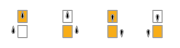
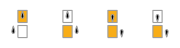
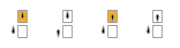
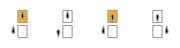
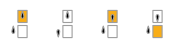
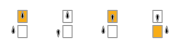
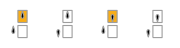
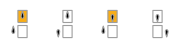
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
254 | 1 | 3 | 3 | 7 | 5 | 7 | 7 | 15 | 9 | 11 | 11 | 15 | 13 | 15 | 15 | 31
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
255 | 1 | 3 | 3 | 7 | 5 | 7 | 7 | 15 | 9 | 11 | 11 | 15 | 13 | 15 | 15 | 31
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
256 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
257 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
258 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
259 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
260 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
261 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 8 | 8 | 0 | 0 | 12 | 0 | 0 | 0
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
262 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
263 | 3 | 7 | 15 | 15 | 7 | 31 | 31 | 31 | 11 | 15 | 63 | 63 | 15 | 63 | 63 | 63
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
264 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
265 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
266 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
267 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
268 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
269 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 0 | 8 | 8 | 8 | 0 | 12 | 8 | 12 | 0
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
270 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
271 | 3 | 7 | 3 | 15 | 7 | 7 | 7 | 31 | 11 | 15 | 11 | 15 | 15 | 15 | 15 | 63
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
272 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
273 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1

```mathematica
Grid[
Flatten[elems,1],
Alignment->Top
]
```

Get rules including the group that does not halt:

```mathematica
eqlgroups=ParallelMap[
First,
GatherBy[
Transpose[{rules,elems[[All,2]]}],
#[[2,2;;-1]]&
],
{2}
];
```

Get rules excluding the group that does not halt:

```mathematica
eqlgroups=ParallelMap[
First,
GatherBy[
Select[
Transpose[{rules,elems[[All,2]]}],
!ContainsOnly[#[[2,2;;-1]],{-1}]&
],
#[[2]]&
],
{2}
];
```

```mathematica
ht[rule_,bits_]:=Table[
Module[{t=0,max=50+2^(Log[2,n]+1)},
NestWhile[
(t++;TuringMachine[rule,#])&,
{{1,bits,0},{IntegerDigits[n,2,bits],0}},
#[[1,3]]<=0&,(* stop when dx > 0, or when x >= 10 *)
1,
max
];
If[t==max,0,t]
],
{n,0,2^bits-1}
]
```

```mathematica
accumulateApply=ResourceFunction["AccumulateApply"];
```

```mathematica
halttimes=ParallelMap[{#,ht[#,bits]}&,eqlgroups,{2}];
```

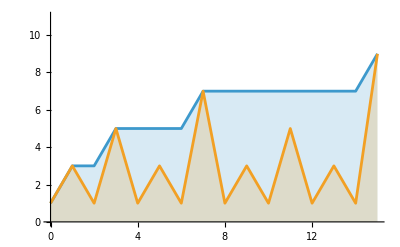
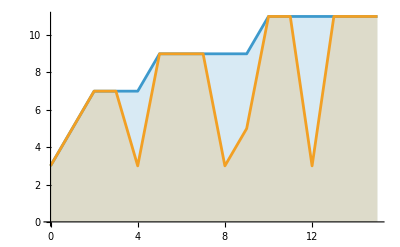
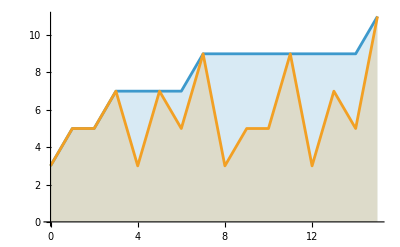
255 | -Graphics- | 9 | {9,9,0}
261 | -Graphics- | 11 | {11,11,0}
263 | -Graphics- | 11 | {11,11,0}
269 | -Graphics- | 11 | {11,11,0}
271 | -Graphics- | 11 | {11,11,0}

```mathematica
Column[
With[{
row=Reap[With[{pfxmax=accumulateApply[Max,#[[2]]]},{
#[[1]],
ListPlot[
{pfxmax,#[[2]]},
DataRange->{0,2^bits-1},
PlotRange->{{0,2^bits-1},{0,Max[Flatten@halttimes[[All,All,2]]]}},
Filling->Axis,
Joined->True
],
Sow[pfxmax[[-1]]]
}
]&/@#](* end With *)
},(* end With init *)
Grid[(* 1D row *)
{With[{minmax=MinMax@row[[2]]},
{
Grid[row[[1]],Spacings->{2, 1}],
{minmax[[1]],minmax[[2]],minmax[[2]]-minmax[[1]]}
}
]},
Spacings->{2,0},
Dividers->{{False,True,False},None}
](* end Row *)
]&/@halttimes,(* end Grid *)
Left,
2,
Dividers->{None,All}
](* end Column *)
```